Auswertung für Praktikum: Luminescence Spectroscopy
Beschreibung

General::ivar: 595. is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

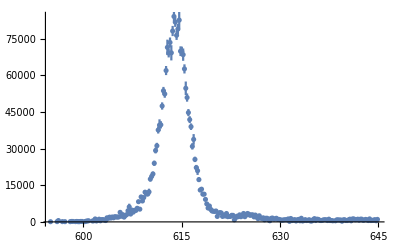

```mathematica
Clear[x];
(* Lade ErrorBar Package *)
Needs["ErrorBarPlots`"];

(* Setze Directory *)
SetDirectory["/Users/chegerland/Desktop/Praktikum_LUM/Messung/"];

(* Importfunktion *)
(* Schneide Datenpunkte mit 0 Fehler raus*)
importdata[data_]:=DeleteCases[
Select[#,UnequalTo[0]]&/@Transpose[{data[[All,2]],data[[All,3]],data[[All,4]]}],
x_/;Length[x]≠3];

(* Fitmodelle Gauß und Doppelgauß *)
model[ampl_,x0_,sigm_,x_]:=ampl*1/Sqrt[2*Pi*sigm^2]*Exp[-(x-x0)^2/(2 sigm^2)];
model2[ampl_,x0_,sigm_,ampl2_,x02_,sigm2_,x_]:=ampl*1/Sqrt[2*Pi*sigm^2]*Exp[-(x-x0)^2/(2 sigm^2)]+ampl2*1/Sqrt[2*Pi*sigm2^2]*Exp[-(x-x02)^2/(2 sigm2^2)];

(* Importiere Daten *)
data1=importdata[Import["80K_1ms.dat"]];

(* Erstelle Fits mit geratenen Peakpositionen *)
f[data_,x0guess_,amplguess_,x02guess_]:={
NonlinearModelFit[Transpose[{data[[All,1]],data[[All,2]]}],model[ampl,x0,sigm,x],{sigm,{x0,x0guess},{ampl,amplguess}},x,Weights->1/data[[All,3]]^2],
NonlinearModelFit[Transpose[{data[[All,1]],data[[All,2]]}],model2[ampl,x0,sigm,ampl2,x02,sigm2,x],{sigm,{x0,x0guess},{ampl,amplguess},ampl2,{x02,x02guess},sigm2},x,Weights->1/data[[All,3]]^2]
};

(* Fit + Datenpunkte mit Fehlerbalken *)
g[data_,x0guess_,amplguess_,x02guess_,index_]:=Show[
ErrorListPlot[data,PlotRange->Full],Plot[f[data,x0guess,amplguess,x02guess][[index]][x],{x,Min[data[[All,1]]],Max[data[[All,1]]]},PlotStyle->Orange,PlotRange->Full]
];

g[data1,615,80000,625,1]

(*(* Fits für Modelle + Parameter-Tabelle *)
nlm = NonlinearModelFit[Transpose[{data1[[All,1]],data1[[All,2]]}],model[ampl,x0,sigm,x],{sigm,{x0,615},{ampl,80000}},x,Weights->1/data[[All,3]]^2];
nlm2 = NonlinearModelFit[Transpose[{data1[[All,1]],data1[[All,2]]}],model2[ampl,x0,sigm,ampl2,x02,sigm2,x],{sigm,{x0,615},{ampl,80000},ampl2,{x02,625},sigm2},x,Weights->1/data[[All,3]]^2];
nlm["ParameterTable"];
nlm2["ParameterTable"];

(* Fit + Datenpunkte mit Fehlerbalken *)
Show[ErrorListPlot[data1,PlotRange->Full],Plot[nlm[x],{x,Min[data1[[All,1]]],Max[data1[[All,1]]]},PlotStyle->Orange,PlotRange->Full]]
Show[ErrorListPlot[data1,PlotRange->Full],Plot[nlm2[x],{x,Min[data1[[All,1]]],Max[data1[[All,1]]]},PlotStyle->Orange,PlotRange->Full]];*)
```